```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/dNinCR/math

## Reverse engineering

```mathematica
η=2β;
```

```mathematica
Clear[ϵ];
ϵ[NN_]=ϵ[NN]/.DSolve[{ϵ'[NN]/ϵ[NN]==η,ϵ[Ni]==ϵi},ϵ[NN],NN][[1]]//Simplify
```

ⅇ^(2 (-Ni+NN) β) ϵi

```mathematica
HinN[NN_]=H[NN]/.DSolve[{(-H'[NN])/H[NN]==ϵ[NN],H[Ni]==Hi},H[NN],NN][[1]]//Simplify
```

ⅇ^(-((-1+ⅇ^(2 (-Ni+NN) β)) ϵi)/(2 β)) Hi

```mathematica
Clear[ϕ]
ϕ[NN_]=ϕ[NN]/.DSolve[{1/2 ϕ'[NN]^2==ϵ[NN],ϕ[Ni]==ϕi},ϕ[NN],NN][[2]]//Simplify
```

(√2 (-1+ⅇ^((-Ni+NN) β)) √ϵi)/β+ϕi

```mathematica
ϕ'[Ni]
```

√2 √ϵi

```mathematica
Ninϕ[x_]=InverseFunction[ϕ][x]//Simplify
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Ni-Log[(√2 √ϵi)/(x β+√2 √ϵi-β ϕi)]/β

```mathematica
ϕ[Ninϕ[x]]//Simplify
```

x

```mathematica
Hinϕ[x_]=HinN[Ninϕ[x]]//Simplify
```

ⅇ^(-1/4 (x-ϕi) (x β+2 √2 √ϵi-β ϕi)) Hi

```mathematica
V[x_]=3 Hinϕ[x]^2-2 Hinϕ'[x]^2//FullSimplify
```

1/2 ⅇ^(-1/2 (x-ϕi) (x β+2 √2 √ϵi-β ϕi)) Hi^2 (6-2 ϵi-β^2 (x-ϕi)^2+2 √2 β √ϵi (-x+ϕi))

```mathematica
H[x_,p_]=Sqrt[(p^2/2+V[x])/3];
```

```mathematica
Vren[x_]=V[Sqrt[2ϵi]/-β x]/.{ϕi->Sqrt[2ϵi]/-β xi}//Simplify
```

-ⅇ^(-((-2+x-xi) (x-xi) ϵi)/β) Hi^2 (-3+(1-x+xi)^2 ϵi)

```mathematica
Hren[x_,p_]=Sqrt[(p^2/2+Vren[x])/3];
```

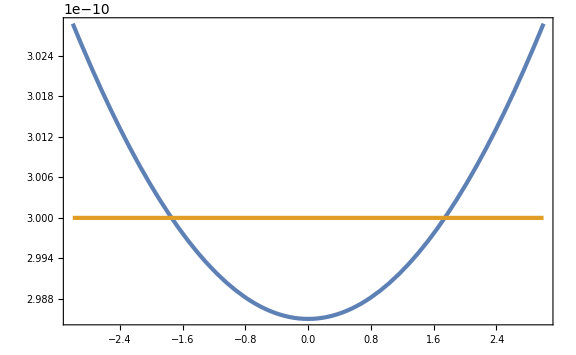

```mathematica
Plot[{Vren[x]/.{Hi->10^-5,ϵi->10^-2,β->-2,xi->-1},Vren[x]/.{Hi->10^-5,ϵi->0,β->-2,xi->-1}},{x,-3,3}]
```

```mathematica
x''[NN]+3 x'[NN]+Vren'[x[NN]]/Hi^2==0//Simplify
```

2 ⅇ^(-(ϵi (xi-x[NN]) (2+xi-x[NN]))/β) ϵi (1+xi-x[NN])+3 x'[NN]+x''[NN]==(2 ⅇ^(-(ϵi (xi-x[NN]) (2+xi-x[NN]))/β) ϵi (1+xi-x[NN]) (-3+(1+xi)^2 ϵi-2 (1+xi) ϵi x[NN]+ϵi x[NN]^2))/β

```mathematica
DSolve[x''[NN]+3 x'[NN]+Vren'[x[NN]]/Hi^2==0//Simplify,x[NN],NN]
```

DSolve[2 ⅇ^(-(ϵi (xi-x[NN]) (2+xi-x[NN]))/β) ϵi (1+xi-x[NN])+3 x'[NN]+x''[NN]==(2 ⅇ^(-(ϵi (xi-x[NN]) (2+xi-x[NN]))/β) ϵi (1+xi-x[NN]) (-3+(1+xi)^2 ϵi-2 (1+xi) ϵi x[NN]+ϵi x[NN]^2))/β,x[NN],NN]

#### β = -1

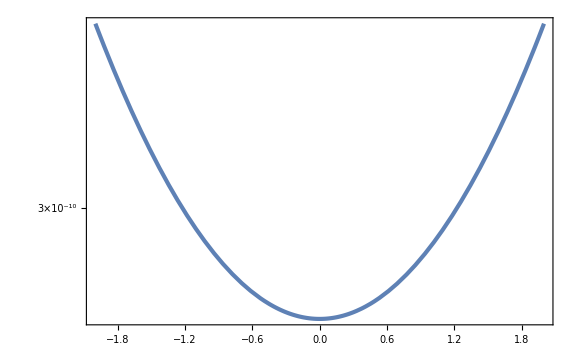

```mathematica
LogPlot[V[Sqrt[2ϵi]/-β x]/.{ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x,-2,2}]
```

```mathematica
tf=50 Hi^-1/.{Hi->10^-5};
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
```

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
Hsol[t_]=H[xsol[t],psol[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t]);
```

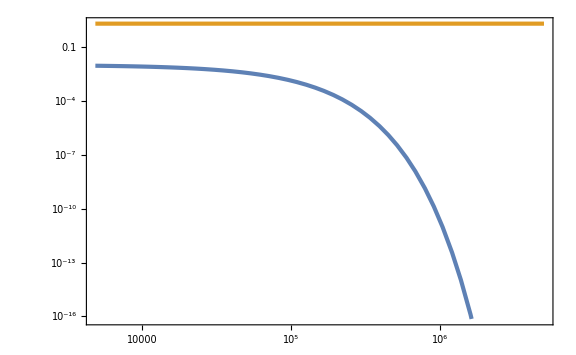

```mathematica
LogLogPlot[{ϵsol[t],-ηsol[t]},{t,0,tf},GridLines->{None,{2}}]
```

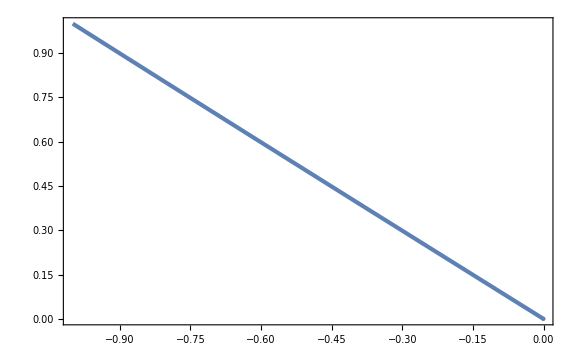

```mathematica
ParametricPlot[{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{t,0,tf},PlotRange->Full]
```

```mathematica
sol1=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol1[t_]=x[t]/.sol1;
psol1[t_]=x'[t]/.sol1;
Hsol1[t_]=H[xsol1[t],psol1[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol1[t_]=psol1[t]^2/(2 Hsol1[t]^2);
ηsol1[t_]=ϵsol1'[t]/(ϵsol1[t]Hsol1[t]);
```

```mathematica
sol2=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol2[t_]=x[t]/.sol2;
psol2[t_]=x'[t]/.sol2;
Hsol2[t_]=H[xsol2[t],psol2[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol2[t_]=psol2[t]^2/(2 Hsol2[t]^2);
ηsol2[t_]=ϵsol2'[t]/(ϵsol2[t]Hsol2[t]);
```

```mathematica
sol3=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol3[t_]=x[t]/.sol3;
psol3[t_]=x'[t]/.sol3;
Hsol3[t_]=H[xsol3[t],psol3[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol3[t_]=psol3[t]^2/(2 Hsol3[t]^2);
ηsol3[t_]=ϵsol3'[t]/(ϵsol3[t]Hsol3[t]);
```

```mathematica
sol4=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol4[t_]=x[t]/.sol4;
psol4[t_]=x'[t]/.sol4;
Hsol4[t_]=H[xsol4[t],psol4[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol4[t_]=psol4[t]^2/(2 Hsol4[t]^2);
ηsol4[t_]=ϵsol4'[t]/(ϵsol4[t]Hsol4[t]);
```

```mathematica
sol5=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol5[t_]=x[t]/.sol5;
psol5[t_]=x'[t]/.sol5;
Hsol5[t_]=H[xsol5[t],psol5[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol5[t_]=psol5[t]^2/(2 Hsol5[t]^2);
ηsol5[t_]=ϵsol5'[t]/(ϵsol5[t]Hsol5[t]);
```

```mathematica
sol6=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol6[t_]=x[t]/.sol6;
psol6[t_]=x'[t]/.sol6;
Hsol6[t_]=H[xsol6[t],psol6[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol6[t_]=psol6[t]^2/(2 Hsol6[t]^2);
ηsol6[t_]=ϵsol6'[t]/(ϵsol6[t]Hsol6[t]);
```

```mathematica
sol7=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol7[t_]=x[t]/.sol7;
psol7[t_]=x'[t]/.sol7;
Hsol7[t_]=H[xsol7[t],psol7[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol7[t_]=psol7[t]^2/(2 Hsol7[t]^2);
ηsol7[t_]=ϵsol7'[t]/(ϵsol7[t]Hsol7[t]);
sol8=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol8[t_]=x[t]/.sol8;
psol8[t_]=x'[t]/.sol8;
Hsol8[t_]=H[xsol8[t],psol8[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol8[t_]=psol8[t]^2/(2 Hsol8[t]^2);
ηsol8[t_]=ϵsol8'[t]/(ϵsol8[t]Hsol8[t]);
sol9=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol9[t_]=x[t]/.sol9;
psol9[t_]=x'[t]/.sol9;
Hsol9[t_]=H[xsol9[t],psol9[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol9[t_]=psol9[t]^2/(2 Hsol9[t]^2);
ηsol9[t_]=ϵsol9'[t]/(ϵsol9[t]Hsol9[t]);
sol10=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol10[t_]=x[t]/.sol10;
psol10[t_]=x'[t]/.sol10;
Hsol10[t_]=H[xsol10[t],psol10[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol10[t_]=psol10[t]^2/(2 Hsol10[t]^2);
ηsol10[t_]=ϵsol10'[t]/(ϵsol10[t]Hsol10[t]);
sol11=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol11[t_]=x[t]/.sol11;
psol11[t_]=x'[t]/.sol11;
Hsol11[t_]=H[xsol11[t],psol11[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-1};
ϵsol11[t_]=psol11[t]^2/(2 Hsol11[t]^2);
ηsol11[t_]=ϵsol11'[t]/(ϵsol11[t]Hsol11[t]);
```

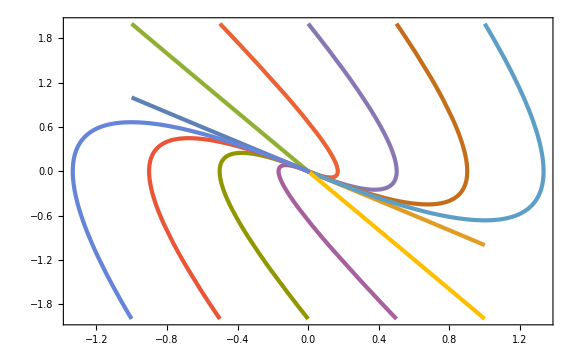

```mathematica
ParametricPlot[{{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol1[t],1/(Sqrt[2ϵi]Hi)psol1[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol2[t],1/(Sqrt[2ϵi]Hi)psol2[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol3[t],1/(Sqrt[2ϵi]Hi)psol3[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol4[t],1/(Sqrt[2ϵi]Hi)psol4[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol5[t],1/(Sqrt[2ϵi]Hi)psol5[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol6[t],1/(Sqrt[2ϵi]Hi)psol6[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol7[t],1/(Sqrt[2ϵi]Hi)psol7[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol8[t],1/(Sqrt[2ϵi]Hi)psol8[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol9[t],1/(Sqrt[2ϵi]Hi)psol9[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol10[t],1/(Sqrt[2ϵi]Hi)psol10[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5},{-β/Sqrt[2ϵi] xsol11[t],1/(Sqrt[2ϵi]Hi)psol11[t]}/.{ϵi->10^-2,β->-1,Hi->10^-5}},{t,0,tf},PlotRange->Full]
```

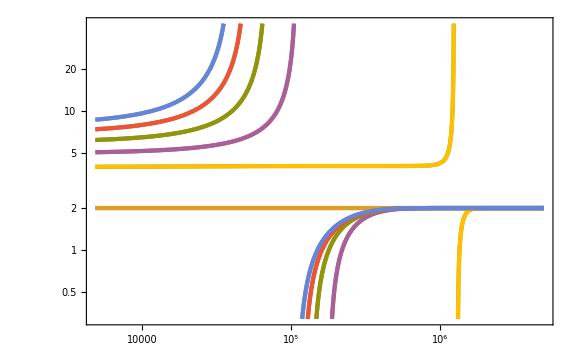

```mathematica
LogLogPlot[{-ηsol[t],-ηsol1[t],-ηsol2[t],-ηsol3[t],-ηsol4[t],-ηsol5[t],-ηsol6[t],-ηsol7[t],-ηsol8[t],-ηsol9[t],-ηsol10[t],-ηsol11[t]},{t,0,tf}]
```

#### β = -3/2

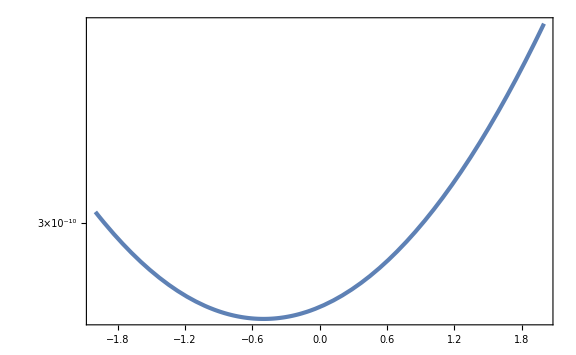

```mathematica
LogPlot[V[Sqrt[2ϵi]/-β x]/.{ϕi->-Sqrt[2 10^-2],ϵi->10^-2,Hi->10^-5,β->-3/2},{x,-2,2}]
```

```mathematica
tf=30 Hi^-1/.{Hi->10^-5};
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
```

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
Hsol[t_]=H[xsol[t],psol[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t]);
```

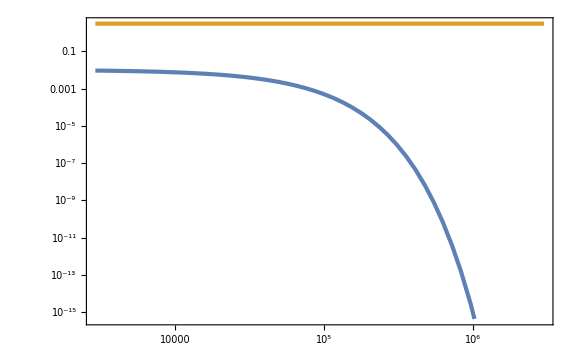

```mathematica
LogLogPlot[{ϵsol[t],-ηsol[t]},{t,0,tf},GridLines->{None,{2}}]
```

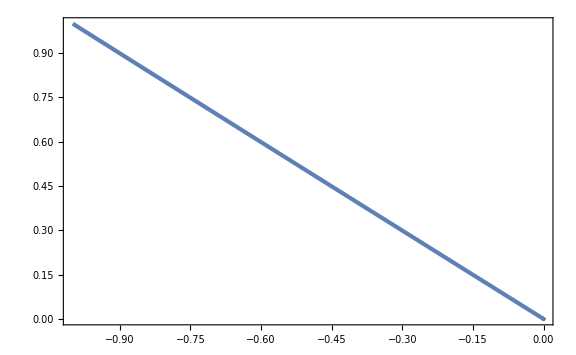

```mathematica
ParametricPlot[{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{t,0,tf},PlotRange->Full]
```

```mathematica
sol1=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol1[t_]=x[t]/.sol1;
psol1[t_]=x'[t]/.sol1;
Hsol1[t_]=H[xsol1[t],psol1[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol1[t_]=psol1[t]^2/(2 Hsol1[t]^2);
ηsol1[t_]=ϵsol1'[t]/(ϵsol1[t]Hsol1[t]);
```

```mathematica
sol2=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol2[t_]=x[t]/.sol2;
psol2[t_]=x'[t]/.sol2;
Hsol2[t_]=H[xsol2[t],psol2[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol2[t_]=psol2[t]^2/(2 Hsol2[t]^2);
ηsol2[t_]=ϵsol2'[t]/(ϵsol2[t]Hsol2[t]);
```

```mathematica
sol3=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol3[t_]=x[t]/.sol3;
psol3[t_]=x'[t]/.sol3;
Hsol3[t_]=H[xsol3[t],psol3[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol3[t_]=psol3[t]^2/(2 Hsol3[t]^2);
ηsol3[t_]=ϵsol3'[t]/(ϵsol3[t]Hsol3[t]);
```

```mathematica
sol4=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol4[t_]=x[t]/.sol4;
psol4[t_]=x'[t]/.sol4;
Hsol4[t_]=H[xsol4[t],psol4[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol4[t_]=psol4[t]^2/(2 Hsol4[t]^2);
ηsol4[t_]=ϵsol4'[t]/(ϵsol4[t]Hsol4[t]);
```

```mathematica
sol5=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol5[t_]=x[t]/.sol5;
psol5[t_]=x'[t]/.sol5;
Hsol5[t_]=H[xsol5[t],psol5[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol5[t_]=psol5[t]^2/(2 Hsol5[t]^2);
ηsol5[t_]=ϵsol5'[t]/(ϵsol5[t]Hsol5[t]);
```

```mathematica
sol6=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol6[t_]=x[t]/.sol6;
psol6[t_]=x'[t]/.sol6;
Hsol6[t_]=H[xsol6[t],psol6[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol6[t_]=psol6[t]^2/(2 Hsol6[t]^2);
ηsol6[t_]=ϵsol6'[t]/(ϵsol6[t]Hsol6[t]);
```

```mathematica
sol7=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol7[t_]=x[t]/.sol7;
psol7[t_]=x'[t]/.sol7;
Hsol7[t_]=H[xsol7[t],psol7[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol7[t_]=psol7[t]^2/(2 Hsol7[t]^2);
ηsol7[t_]=ϵsol7'[t]/(ϵsol7[t]Hsol7[t]);
```

```mathematica
sol8=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol8[t_]=x[t]/.sol8;
psol8[t_]=x'[t]/.sol8;
Hsol8[t_]=H[xsol8[t],psol8[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol8[t_]=psol8[t]^2/(2 Hsol8[t]^2);
ηsol8[t_]=ϵsol8'[t]/(ϵsol8[t]Hsol8[t]);
```

```mathematica
sol9=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol9[t_]=x[t]/.sol9;
psol9[t_]=x'[t]/.sol9;
Hsol9[t_]=H[xsol9[t],psol9[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol9[t_]=psol9[t]^2/(2 Hsol9[t]^2);
ηsol9[t_]=ϵsol9'[t]/(ϵsol9[t]Hsol9[t]);
```

```mathematica
sol10=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol10[t_]=x[t]/.sol10;
psol10[t_]=x'[t]/.sol10;
Hsol10[t_]=H[xsol10[t],psol10[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol10[t_]=psol10[t]^2/(2 Hsol10[t]^2);
ηsol10[t_]=ϵsol10'[t]/(ϵsol10[t]Hsol10[t]);
```

```mathematica
sol11=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==-2Hi ϕ'[Ni]}/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol11[t_]=x[t]/.sol11;
psol11[t_]=x'[t]/.sol11;
Hsol11[t_]=H[xsol11[t],psol11[t]]/.{Ni->0,ϕi->-Sqrt[2 10^-2] 2/3,ϵi->10^-2,Hi->10^-5,β->-3/2};
ϵsol11[t_]=psol11[t]^2/(2 Hsol11[t]^2);
ηsol11[t_]=ϵsol11'[t]/(ϵsol11[t]Hsol11[t]);
```

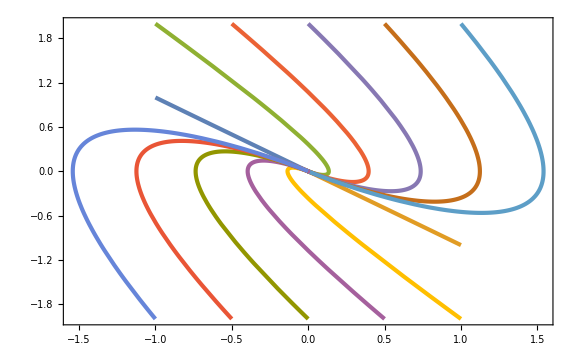

```mathematica
ParametricPlot[{{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol1[t],1/(Sqrt[2ϵi]Hi)psol1[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol2[t],1/(Sqrt[2ϵi]Hi)psol2[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol3[t],1/(Sqrt[2ϵi]Hi)psol3[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol4[t],1/(Sqrt[2ϵi]Hi)psol4[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol5[t],1/(Sqrt[2ϵi]Hi)psol5[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol6[t],1/(Sqrt[2ϵi]Hi)psol6[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol7[t],1/(Sqrt[2ϵi]Hi)psol7[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol8[t],1/(Sqrt[2ϵi]Hi)psol8[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol9[t],1/(Sqrt[2ϵi]Hi)psol9[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol10[t],1/(Sqrt[2ϵi]Hi)psol10[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol11[t],1/(Sqrt[2ϵi]Hi)psol11[t]}/.{ϵi->10^-2,β->-3/2,Hi->10^-5}},{t,0,tf},PlotRange->Full]
```

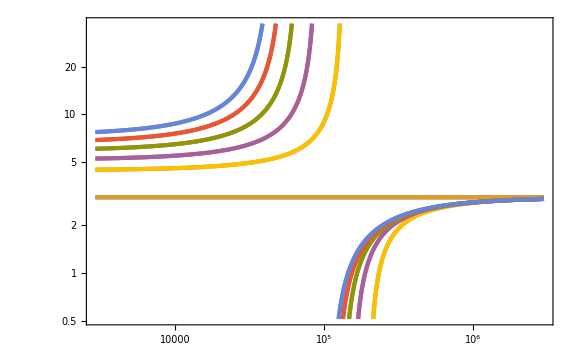

```mathematica
LogLogPlot[{-ηsol[t],-ηsol1[t],-ηsol2[t],-ηsol3[t],-ηsol4[t],-ηsol5[t],-ηsol6[t],-ηsol7[t],-ηsol8[t],-ηsol9[t],-ηsol10[t],-ηsol11[t]},{t,0,tf}]
```

#### β = -2

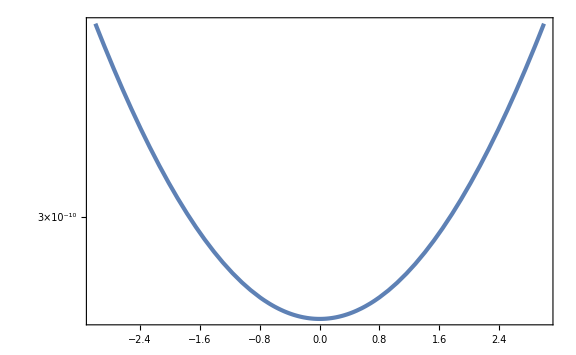

```mathematica
LogPlot[V[Sqrt[2ϵi]/-β x]/.{ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x,-3,3}]
```

```mathematica
tf=10 Hi^-1/.{Hi->10^-5};
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
```

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
Hsol[t_]=H[xsol[t],psol[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t]);
```

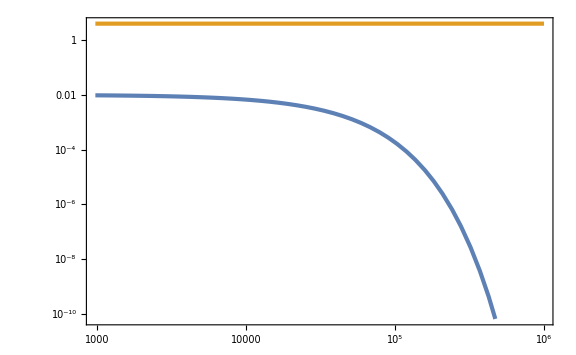

```mathematica
LogLogPlot[{ϵsol[t],-ηsol[t]},{t,0,tf},GridLines->{None,{4}}]
```

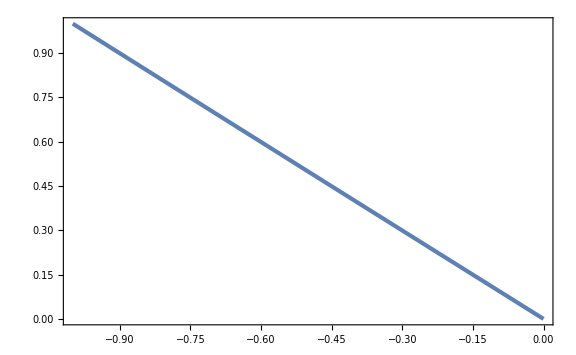

```mathematica
ParametricPlot[{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{t,0,tf},PlotRange->Full]
```

```mathematica
sol1=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol1[t_]=x[t]/.sol1;
psol1[t_]=x'[t]/.sol1;
Hsol1[t_]=H[xsol1[t],psol1[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol1[t_]=psol1[t]^2/(2 Hsol1[t]^2);
ηsol1[t_]=ϵsol1'[t]/(ϵsol1[t]Hsol1[t]);
```

```mathematica
sol2=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol2[t_]=x[t]/.sol2;
psol2[t_]=x'[t]/.sol2;
Hsol2[t_]=H[xsol2[t],psol2[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol2[t_]=psol2[t]^2/(2 Hsol2[t]^2);
ηsol2[t_]=ϵsol2'[t]/(ϵsol2[t]Hsol2[t]);
```

```mathematica
sol3=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol3[t_]=x[t]/.sol3;
psol3[t_]=x'[t]/.sol3;
Hsol3[t_]=H[xsol3[t],psol3[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol3[t_]=psol3[t]^2/(2 Hsol3[t]^2);
ηsol3[t_]=ϵsol3'[t]/(ϵsol3[t]Hsol3[t]);
```

```mathematica
sol4=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol4[t_]=x[t]/.sol4;
psol4[t_]=x'[t]/.sol4;
Hsol4[t_]=H[xsol4[t],psol4[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol4[t_]=psol4[t]^2/(2 Hsol4[t]^2);
ηsol4[t_]=ϵsol4'[t]/(ϵsol4[t]Hsol4[t]);
```

```mathematica
sol5=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol5[t_]=x[t]/.sol5;
psol5[t_]=x'[t]/.sol5;
Hsol5[t_]=H[xsol5[t],psol5[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/2,ϵi->10^-2,Hi->10^-5,β->-2};
ϵsol5[t_]=psol5[t]^2/(2 Hsol5[t]^2);
ηsol5[t_]=ϵsol5'[t]/(ϵsol5[t]Hsol5[t]);
```

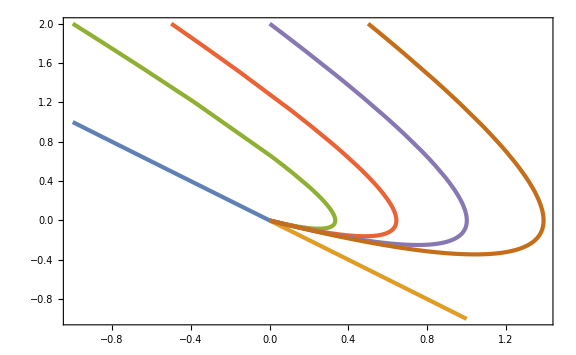

```mathematica
ParametricPlot[{{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol1[t],1/(Sqrt[2ϵi]Hi)psol1[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol2[t],1/(Sqrt[2ϵi]Hi)psol2[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol3[t],1/(Sqrt[2ϵi]Hi)psol3[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol4[t],1/(Sqrt[2ϵi]Hi)psol4[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5},{-β/Sqrt[2ϵi] xsol5[t],1/(Sqrt[2ϵi]Hi)psol5[t]}/.{ϵi->10^-2,β->-2,Hi->10^-5}},{t,0,tf},PlotRange->Full]
```

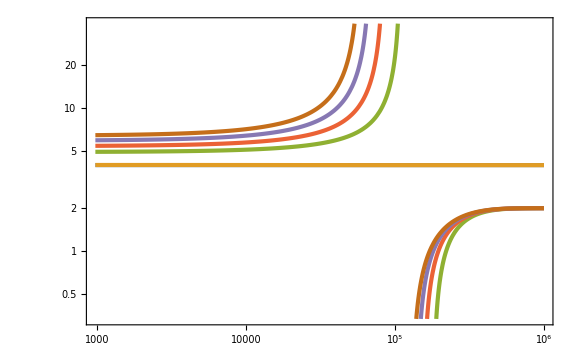

```mathematica
LogLogPlot[{-ηsol[t],-ηsol1[t],-ηsol2[t],-ηsol3[t],-ηsol4[t],-ηsol5[t]},{t,0,tf}]
```

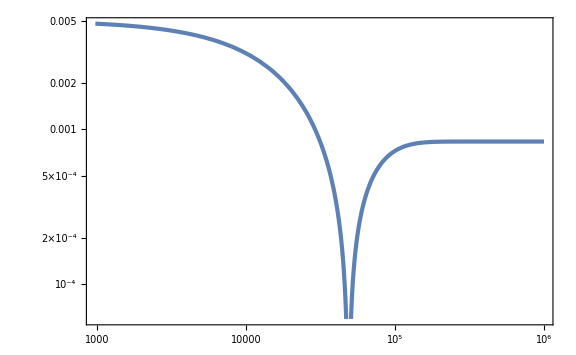

```mathematica
LogLogPlot[{Abs[(xsol1''[t]-β Hsol1[t] xsol1'[t])/xsol1''[t]/.{β->-2}]},{t,0,tf}]
```

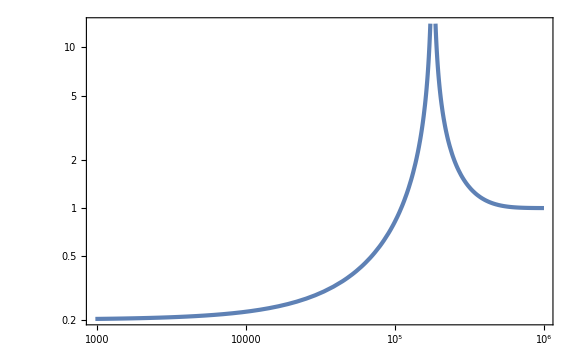

```mathematica
LogLogPlot[{Abs[(xsol2''[t]-β Hsol2[t] xsol2'[t])/xsol2''[t]/.{β->-2}]},{t,0,tf}]
```

#### β = -3

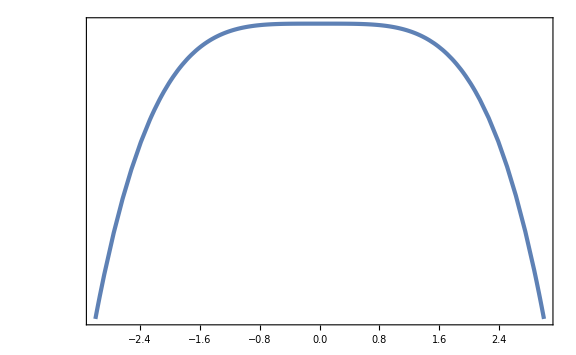

```mathematica
LogPlot[V[Sqrt[2ϵi]/-β x]/.{ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x,-3,3}]
```

```mathematica
tf=10 Hi^-1/.{Hi->10^-5};
sol=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
```

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
Hsol[t_]=H[xsol[t],psol[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t]);
```

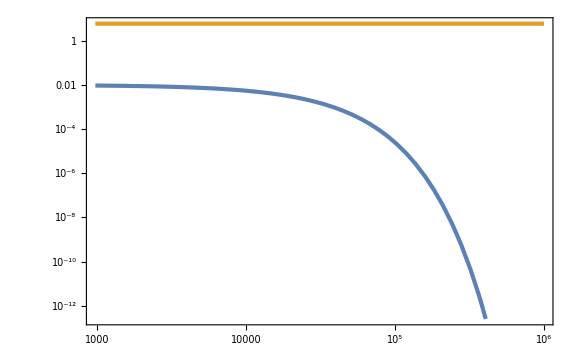

```mathematica
LogLogPlot[{ϵsol[t],-ηsol[t]},{t,0,tf},GridLines->{None,{2}}]
```

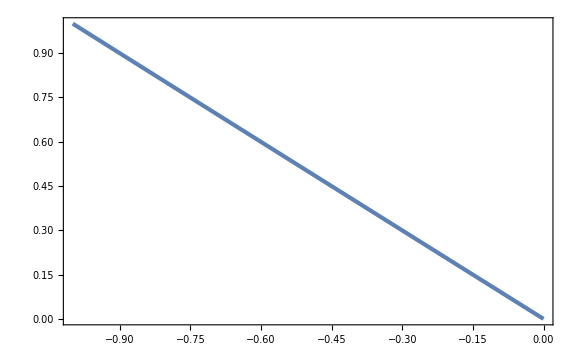

```mathematica
ParametricPlot[{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{t,0,tf},PlotRange->Full]
```

```mathematica
sol1=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==-ϕ[0],x'[0]==-Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol1[t_]=x[t]/.sol1;
psol1[t_]=x'[t]/.sol1;
Hsol1[t_]=H[xsol1[t],psol1[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol1[t_]=psol1[t]^2/(2 Hsol1[t]^2);
ηsol1[t_]=ϵsol1'[t]/(ϵsol1[t]Hsol1[t]);
```

```mathematica
sol2=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0],x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->70][[1]];
xsol2[t_]=x[t]/.sol2;
psol2[t_]=x'[t]/.sol2;
Hsol2[t_]=H[xsol2[t],psol2[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol2[t_]=psol2[t]^2/(2 Hsol2[t]^2);
ηsol2[t_]=ϵsol2'[t]/(ϵsol2[t]Hsol2[t]);
```

```mathematica
sol3=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==ϕ[0]/2,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->50][[1]];
xsol3[t_]=x[t]/.sol3;
psol3[t_]=x'[t]/.sol3;
Hsol3[t_]=H[xsol3[t],psol3[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol3[t_]=psol3[t]^2/(2 Hsol3[t]^2);
ηsol3[t_]=ϵsol3'[t]/(ϵsol3[t]Hsol3[t]);
```

```mathematica
sol4=NDSolve[{x''[t]+3H[x[t],x'[t]]x'[t]+V'[x[t]]==0,x[0]==0,x'[0]==2Hi ϕ'[Ni]}/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3},{x[t],x'[t]},{t,0,tf},WorkingPrecision->60][[1]];
xsol4[t_]=x[t]/.sol4;
psol4[t_]=x'[t]/.sol4;
Hsol4[t_]=H[xsol4[t],psol4[t]]/.{Ni->0,ϕi->(-Sqrt[2 10^-2])/3,ϵi->10^-2,Hi->10^-5,β->-3};
ϵsol4[t_]=psol4[t]^2/(2 Hsol4[t]^2);
ηsol4[t_]=ϵsol4'[t]/(ϵsol4[t]Hsol4[t]);
```

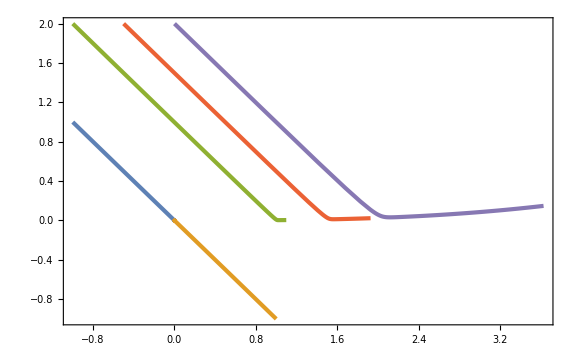

```mathematica
ParametricPlot[{{-β/Sqrt[2ϵi] xsol[t],1/(Sqrt[2ϵi]Hi)psol[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{-β/Sqrt[2ϵi] xsol1[t],1/(Sqrt[2ϵi]Hi)psol1[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{-β/Sqrt[2ϵi] xsol2[t],1/(Sqrt[2ϵi]Hi)psol2[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{-β/Sqrt[2ϵi] xsol3[t],1/(Sqrt[2ϵi]Hi)psol3[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5},{-β/Sqrt[2ϵi] xsol4[t],1/(Sqrt[2ϵi]Hi)psol4[t]}/.{ϵi->10^-2,β->-3,Hi->10^-5}},{t,0,tf},PlotRange->Full]
```

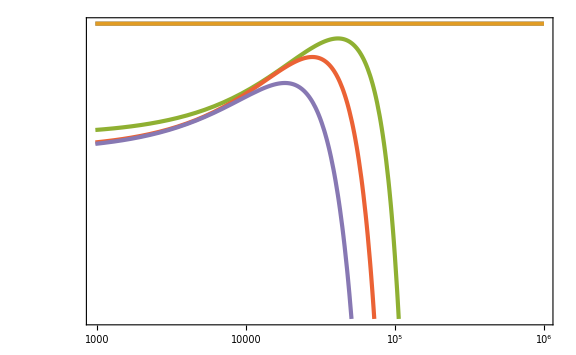

```mathematica
LogLogPlot[{-ηsol[t],-ηsol1[t],-ηsol2[t],-ηsol3[t],-ηsol4[t]},{t,0,tf}]
```

### SR2USR2SR

```mathematica
$Assumptions={ϵi>0,β<0,Ne>Ns};
```

```mathematica
η1[NN_]=0;
η2[NN_]=2β;
η3[NN_]=0;
```

```mathematica
lnϵ1[NN_]=Integrate[η1[Np],{Np,0,NN}]+Log[ϵi]
lnϵ2[NN_]=Integrate[η2[Np],{Np,Ns,NN}]+lnϵ1[Ns]
lnϵ3[NN_]=Integrate[η3[Np],{Np,Ne,NN}]+lnϵ2[Ne]
```

Log[ϵi]

2 (NN-Ns) β+Log[ϵi]

2 (Ne-Ns) β+Log[ϵi]

```mathematica
ϵ1[NN_]=Exp[lnϵ1[NN]]
ϵ2[NN_]=Exp[lnϵ2[NN]]
ϵ3[NN_]=Exp[lnϵ3[NN]]
```

ϵi

ⅇ^(2 (NN-Ns) β) ϵi

ⅇ^(2 (Ne-Ns) β) ϵi

```mathematica
dϕdN1[NN_]=Sqrt[2ϵ1[NN]]//Simplify
dϕdN2[NN_]=Simplify[Sqrt[2ϵ2[NN]],{NN>Ns}]
dϕdN3[NN_]=Sqrt[2ϵ3[NN]]//Simplify
```

√2 √ϵi

√2 ⅇ^((NN-Ns) β) √ϵi

√2 ⅇ^((Ne-Ns) β) √ϵi

```mathematica
ϕ1[NN_]=Integrate[dϕdN1[Np],{Np,0,NN}]
ϕ2[NN_]=Integrate[dϕdN2[Np],{Np,Ns,NN}]+ϕ1[Ns]//Simplify
ϕ3[NN_]=Integrate[dϕdN3[Np],{Np,Ne,NN}]+ϕ2[Ne]//Simplify
```

√2 NN √ϵi

(√2 (-1+ⅇ^((NN-Ns) β)+Ns β) √ϵi)/β

(√2 (-1+Ns β+ⅇ^((Ne-Ns) β) (1-Ne β+NN β)) √ϵi)/β

```mathematica
N1[ϕ_]=InverseFunction[ϕ1][ϕ]
N2[ϕ_]=InverseFunction[ϕ2][ϕ]//Simplify
N3[ϕ_]=InverseFunction[ϕ3][ϕ]//Simplify
```

ϕ/(√2 √ϵi)

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Ns-Log[-(√2 √ϵi)/(√2 (-1+Ns β) √ϵi-β ϕ)]/β

Ne-1/β+ⅇ^((-Ne+Ns) β) (-Ns+1/β+ϕ/(√2 √ϵi))

```mathematica
lnH1[NN_]=-Integrate[ϵ1[Np],{Np,0,NN}]+Log[Hi]
lnH2[NN_]=-Integrate[ϵ2[Np],{Np,Ns,NN}]+lnH1[Ns]
lnH3[NN_]=-Integrate[ϵ3[Np],{Np,Ne,NN}]+lnH2[Ne]
```

-NN ϵi+Log[Hi]

-Ns ϵi-((-1+ⅇ^(2 (NN-Ns) β)) ϵi)/(2 β)+Log[Hi]

-ⅇ^(2 (Ne-Ns) β) (-Ne+NN) ϵi-Ns ϵi-((-1+ⅇ^(2 (Ne-Ns) β)) ϵi)/(2 β)+Log[Hi]

```mathematica
H1[NN_]=Exp[lnH1[NN]]
H2[NN_]=Exp[lnH2[NN]]
H3[NN_]=Exp[lnH3[NN]]
```

ⅇ^(-NN ϵi) Hi

ⅇ^(-Ns ϵi-((-1+ⅇ^(2 (NN-Ns) β)) ϵi)/(2 β)) Hi

ⅇ^(-ⅇ^(2 (Ne-Ns) β) (-Ne+NN) ϵi-Ns ϵi-((-1+ⅇ^(2 (Ne-Ns) β)) ϵi)/(2 β)) Hi

```mathematica
H1ofϕ[ϕ_]=H1[N1[ϕ]]
H2ofϕ[ϕ_]=H2[N2[ϕ]]//Simplify
H3ofϕ[ϕ_]=H3[N3[ϕ]]//Simplify
```

ⅇ^(-(√ϵi ϕ)/(√2)) Hi

ⅇ^(-1/2 Ns^2 β ϵi+(Ns β √ϵi ϕ)/(√2)-1/4 ϕ (2 √2 √ϵi+β ϕ)) Hi

ⅇ^(((-1+ⅇ^((Ne-Ns) β)) (-1+ⅇ^((Ne-Ns) β)+2 Ns β) ϵi)/(2 β)-(ⅇ^((Ne-Ns) β) √ϵi ϕ)/(√2)) Hi

```mathematica
-1/2 Ns^2 β ϵi+(Ns β √ϵi ϕ)/(√2)-1/4 ϕ (2 √2 √ϵi+β ϕ)-(-(ϵi β)/2(ϕ/Sqrt[2ϵi]-Ns)^2-Sqrt[ϵi/2]ϕ)//Simplify
```

0

```mathematica
((-1+ⅇ^((Ne-Ns) β)) (-1+ⅇ^((Ne-Ns) β)+2 Ns β) ϵi)/(2 β)-(ⅇ^((Ne-Ns) β) √ϵi ϕ)/(√2)-(-ϵi E^(β(Ne-Ns))(ϕ/Sqrt[2ϵi]-1/β(E^(β(Ne-Ns))-1)-Ns)-ϵi/(2β)(E^(2β(Ne-Ns))-1)-ϵi Ns)//Simplify
```

0

```mathematica
V1[ϕ_]=3 H1ofϕ[ϕ]^2-2 H1ofϕ'[ϕ]^2//Simplify
V2[ϕ_]=3 H2ofϕ[ϕ]^2-2 H2ofϕ'[ϕ]^2//Simplify
V3[ϕ_]=3 H3ofϕ[ϕ]^2-2 H3ofϕ'[ϕ]^2//Simplify
```

-ⅇ^(-√2 √ϵi ϕ) Hi^2 (-3+ϵi)

-1/2 ⅇ^(-Ns^2 β ϵi+√2 Ns β √ϵi ϕ-1/2 ϕ (2 √2 √ϵi+β ϕ)) Hi^2 (-6+2 (-1+Ns β)^2 ϵi-2 √2 β (-1+Ns β) √ϵi ϕ+β^2 ϕ^2)

-ⅇ^(((-1+ⅇ^((Ne-Ns) β)) (-1+ⅇ^((Ne-Ns) β)+2 Ns β) ϵi)/β-√2 ⅇ^((Ne-Ns) β) √ϵi ϕ) Hi^2 (-3+ⅇ^(2 (Ne-Ns) β) ϵi)

```mathematica
V1[ϕ2[Ns]]//Simplify
V2[ϕ2[Ns]]//Simplify
```

-ⅇ^(-2 Ns ϵi) Hi^2 (-3+ϵi)

-ⅇ^(-2 Ns ϵi) Hi^2 (-3+ϵi)

```mathematica
Normal[Series[V1[x],{ϵi,0,1}]]//Simplify
Normal[Series[V2[x],{ϵi,0,0}]]//Simplify
Normal[Series[V3[x],{ϵi,0,1}]]//Simplify
```

-Hi^2 (-3+3 √2 x √ϵi+ϵi-3 x^2 ϵi)

-1/2 ⅇ^(-(x^2 β)/2) Hi^2 (-6+x^2 β^2)

(Hi^2 (3 (-1+ⅇ^((Ne-Ns) β))^2 ϵi+β (3-6 Ns ϵi+ⅇ^(2 (Ne-Ns) β) (-1+3 x^2) ϵi+ⅇ^((Ne-Ns) β) (-3 √2 x √ϵi+6 Ns ϵi))))/β

```mathematica
TeXForm[V2[ϕ]]
```

-\frac{1}{2} \text{Hi}^2 \left(\beta ^2 \phi ^2-2 \sqrt{2} \beta  \sqrt{\text{$\epsilon $i}} \phi  (\beta 
   \text{Ns}-1)+2 \text{$\epsilon $i} (\beta  \text{Ns}-1)^2-6\right) \exp \left(-\frac{1}{2} \phi  \left(\beta
    \phi +2 \sqrt{2} \sqrt{\text{$\epsilon $i}}\right)-\beta  \text{Ns}^2 \text{$\epsilon $i}+\sqrt{2} \beta 
   \text{Ns} \sqrt{\text{$\epsilon $i}} \phi \right)

```mathematica
TeXForm[V3[ϕ]]
```

\text{Hi}^2 \left(\text{$\epsilon $i} e^{2 \beta  (\text{Ne}-\text{Ns})}-3\right) \left(-\exp
   \left(\frac{\text{$\epsilon $i} \left(e^{\beta  (\text{Ne}-\text{Ns})}-1\right) \left(e^{\beta 
   (\text{Ne}-\text{Ns})}+2 \beta  \text{Ns}-1\right)}{\beta }-\sqrt{2} \sqrt{\text{$\epsilon $i}} \phi 
   e^{\beta  (\text{Ne}-\text{Ns})}\right)\right)

```mathematica
βs=-2;
ϵis=10^-2;
His=10^-5;
Nss=5;
Nes=7;
ϕss=ϕ1[Nss]/.{ϵi->ϵis}
ϕes=ϕ2[Nes]/.{Ns->Nss,ϵi->ϵis,β->βs}
```

1/(√2)

-(-11+1/ⅇ^4)/(10 √2)

```mathematica
V1s[ϕ_]=V1[ϕ]/.{ϵi->ϵis,Hi->His}
V2s[ϕ_]=V2[ϕ]/.{ϵi->ϵis,Hi->His,Ns->Nss,β->βs}
V3s[ϕ_]=V3[ϕ]/.{ϵi->ϵis,Hi->His,Ns->Nss,Ne->Nes,β->βs}
```

(299 ⅇ^(-ϕ/(5 √2)))/1000000000000

-(ⅇ^(1/2-√2 ϕ-1/2 ((√2)/5-2 ϕ) ϕ) (-179/50-(22 √2 ϕ)/5+4 ϕ^2))/20000000000

-((-3+1/(100 ⅇ^8)) ⅇ^(-1/200 (-21+1/ⅇ^4) (-1+1/ⅇ^4)-ϕ/(5 √2 ⅇ^4)))/10000000000

```mathematica
Vs[ϕ_]=V1s[ϕ]UnitStep[ϕss-ϕ]+V2s[ϕ]UnitStep[ϕes-ϕ,ϕ-ϕss]+V3s[ϕ]UnitStep[ϕ-ϕes]
Vps[ϕ_]=V1s'[ϕ]UnitStep[ϕss-ϕ]+V2s'[ϕ]UnitStep[ϕes-ϕ,ϕ-ϕss]+V3s'[ϕ]UnitStep[ϕ-ϕes]
```

(299 ⅇ^(-ϕ/(5 √2)) UnitStep[1/(√2)-ϕ])/1000000000000-((-3+1/(100 ⅇ^8)) ⅇ^(-1/200 (-21+1/ⅇ^4) (-1+1/ⅇ^4)-ϕ/(5 √2 ⅇ^4)) UnitStep[(-11+1/ⅇ^4)/(10 √2)+ϕ])/10000000000-(ⅇ^(1/2-√2 ϕ-1/2 ((√2)/5-2 ϕ) ϕ) (-179/50-(22 √2 ϕ)/5+4 ϕ^2) UnitStep[-(-11+1/ⅇ^4)/(10 √2)-ϕ,-1/(√2)+ϕ])/20000000000

-(299 ⅇ^(-ϕ/(5 √2)) UnitStep[1/(√2)-ϕ])/(5000000000000 √2)+((-3+1/(100 ⅇ^8)) ⅇ^(-4-1/200 (-21+1/ⅇ^4) (-1+1/ⅇ^4)-ϕ/(5 √2 ⅇ^4)) UnitStep[(-11+1/ⅇ^4)/(10 √2)+ϕ])/(50000000000 √2)+(-(ⅇ^(1/2-√2 ϕ-1/2 ((√2)/5-2 ϕ) ϕ) (-(22 √2)/5+8 ϕ))/20000000000-(ⅇ^(1/2-√2 ϕ-1/2 ((√2)/5-2 ϕ) ϕ) (-179/50-(22 √2 ϕ)/5+4 ϕ^2) (-√2+ϕ+1/2 (-(√2)/5+2 ϕ)))/20000000000) UnitStep[-(-11+1/ⅇ^4)/(10 √2)-ϕ,-1/(√2)+ϕ]

```mathematica
ϕes//N
```

0.776522

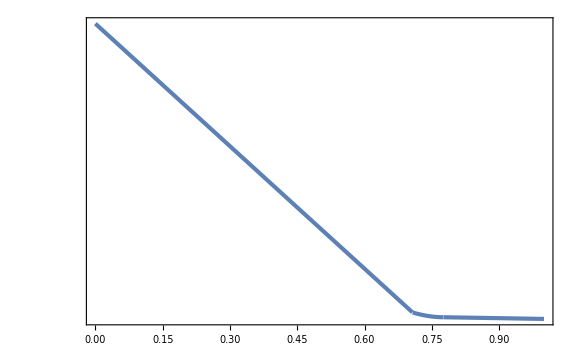

```mathematica
LogPlot[Vs[ϕ],{ϕ,0,1}]
```

```mathematica
Hs[x_,p_]=Sqrt[(p^2/2+Vs[x])/3];
```

```mathematica
tf=10 His^-1;
sol=NDSolve[{x''[t]+3Hs[x[t],x'[t]]x'[t]+Vps[x[t]]==0,x[0]==0,x'[0]==Sqrt[2ϵis]His,
NN'[t]==Hs[x[t],x'[t]],NN[0]==0},{x[t],x'[t],NN[t]},{t,0,tf},WorkingPrecision->50][[1]]
```

{x[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],NN[t]→InterpolatingFunction[…][t]}

```mathematica
xsol[t_]=x[t]/.sol;
psol[t_]=x'[t]/.sol;
pdotsol[t_]=x''[t]/.sol;
Nsol[t_]=NN[t]/.sol;
Hsol[t_]=Hs[xsol[t],psol[t]];
ϵsol[t_]=psol[t]^2/(2 Hsol[t]^2);
ηsol[t_]=ϵsol'[t]/(ϵsol[t]Hsol[t])(*2 pdotsol[t]/(Hsol[t]psol[t])+psol[t]^2/Hsol[t]^2*);
```

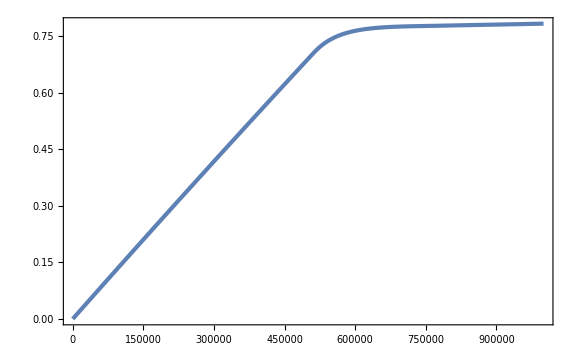

```mathematica
Plot[xsol[t],{t,0,tf}]
```

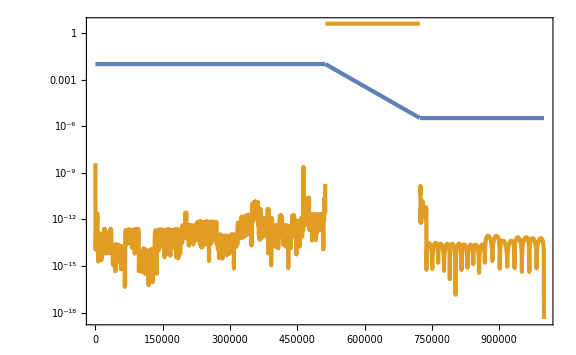

```mathematica
LogPlot[{ϵsol[t],Abs[ηsol[t]]},{t,0,tf}]
```

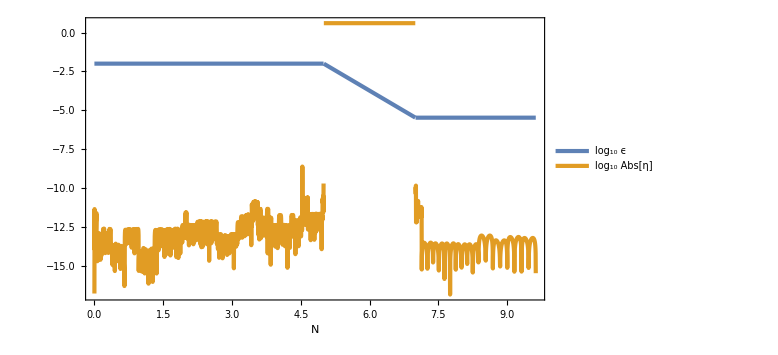

```mathematica
ParametricPlot[{{Nsol[t],Log10[ϵsol[t]]},{Nsol[t],Log10[Abs[ηsol[t]]]}},{t,0,tf},FrameLabel->{N,None},PlotLegends->Placed[LineLegend[{"log_10 ϵ",Subscript[log, 10] Abs[η]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.87,0.87}]]
```

## Analytic

```mathematica
V[x_]=3 M^2(1-(3+β)/6(1-Cosh[Sqrt[-2β]x]));
```

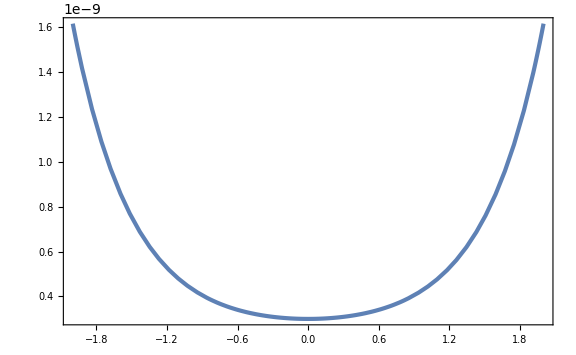

```mathematica
Plot[V[x]/.{M->10^-5,β->-2},{x,-2,2}]
```

```mathematica
H[x_,p_]=Sqrt[(p^2/2+V[x])/3];
```

```mathematica
x''[NN]+3 x'[NN]+V'[x[NN]]/M^2==0//Simplify
```

(√-β (3+β) Sinh[√2 √-β x[NN]])/(√2)+3 x'[NN]+x''[NN]==0

```mathematica
DSolve[x''[NN]+3 x'[NN]+V'[x[NN]]/M^2==0/.{β->-2},x[NN],NN]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve[Sinh[2 x[NN]]+3 x'[NN]+x''[NN]==0,x[NN],NN]

## Gumbel

```mathematica
zeta[x_]=-1/γ Log[1-γ μ Sinc[x]];
```

```mathematica
CompactC[x_]=2/3(1-(1+x zeta'[x])^2)//Simplify
```

2/3 (1-(1+(μ (x Cos[x]-Sin[x]))/(x-x γ μ Sinc[x]))^2)

```mathematica
Normal[Series[CompactC[x],{x,0,2}]]
```

-(4 x^2 μ)/(9 (-1+γ μ))

```mathematica
rmcond[x_]=zeta'[x]+x zeta''[x]//Simplify
```

1/(x^3 (-1+γ μ Sinc[x])^2)μ (x^2 γ μ Cos[x]^2+Sin[x] (x-x^3+γ μ Sin[x])-x Cos[x] (x+2 γ μ Sin[x])+x γ μ (x Cos[x]+(-1+x^2) Sin[x]) Sinc[x])

```mathematica
xm[d_]=Normal[Series[x/.Solve[Normal[Series[rmcond[x]==0/.{μ->(1-d)/γ},{d,0,1},{x,0,1}]]//Simplify,x][[4]],{d,0,1}]]
```

2^(3/4) 15^(1/4) d^(1/4)

```mathematica
Cm[γ_]=Normal[Series[CompactC[xm[d]]/.{μ->(1-d)/γ},{d,0,0}]]//Simplify
```

(8 (-1+γ))/(3 γ^2)

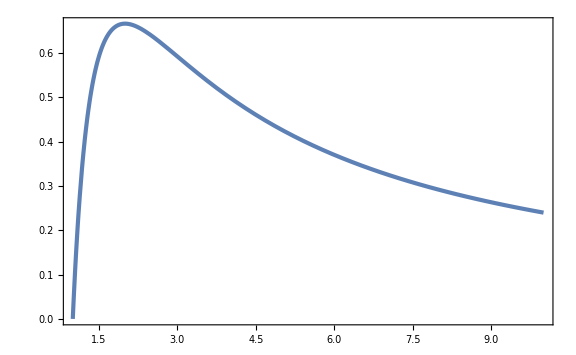

```mathematica
Plot[Cm[γ],{γ,1,10}]
```

```mathematica
arealR[x_]=x E^zeta[x]
```

x (1-γ μ Sinc[x])^(-1/γ)

```mathematica
Cintegrand[x_]=Normal[Series[CompactC[x] arealR[x]^2 arealR'[x]/.{μ->(1-d)/γ},{d,0,0},{x,0,2}]]
```

(2^(3+3/γ) 3^(-1+3/γ) (x^2)^(1-3/γ) (-2+γ) (-1+γ))/γ^3

```mathematica
Integrate[Cintegrand[x],{x,0,xm[d]},Assumptions->{γ>2}]
```

(2^(3/4 (7-2/γ)) 3^(-5/4+3/(2 γ)) 5^((3 (-2+γ))/(4 γ)) d^((3 (-2+γ))/(4 γ)) (-1+γ))/γ^2

```mathematica
C0=Normal[Series[3/arealR[xm[d]]^3 Integrate[Cintegrand[x],{x,0,xm[d]},Assumptions->{γ>2}]/.{μ->(1-d)/γ},{d,0,0}]]//Simplify
C1=D[Normal[Series[3/arealR[xm[d]]^3 Integrate[Cintegrand[x],{x,0,xm[d]},Assumptions->{γ>2}]/.{μ->(1-d)/γ},{d,0,1}]], d]/.{d->0}//Simplify
Cbarm[d_]=C0+C1 d
```

(8 (-1+γ))/(3 γ^2)

-(48 (-1+γ))/(7 γ^3)

-(48 d (-1+γ))/(7 γ^3)+(8 (-1+γ))/(3 γ^2)

```mathematica
Solve[C0==2/5,γ]
```

{{γ→2/3 (5-√10)},{γ→2/3 (5+√10)}}

```mathematica
dsol[γ_]=d/.Solve[Cbarm[d]==2/5,d][[1]]
```

-(7 γ (20-20 γ+3 γ^2))/(360 (-1+γ))

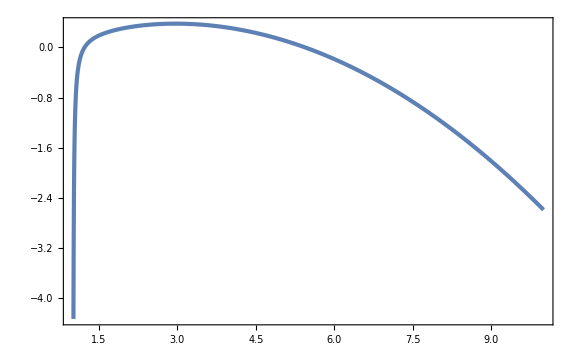

```mathematica
Plot[dsol[γ],{γ,1,10}]
```

```mathematica
dsol[5.44]
```

0.000457417

```mathematica
γmax=γ/.Solve[dsol[γ]==0,γ][[3]]
```

2/3 (5+√10)

```mathematica
γmax//N
```

5.44152

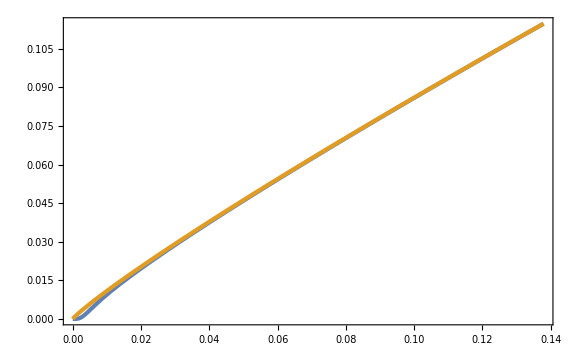

```mathematica
Plot[{CompactC[x] arealR[x]^2 arealR'[x]/.{μ->(1-dsol[γ])/γ}/.{γ->γmax-10^-5},Cintegrand[x]/.{γ->γmax-10^-5}},{x,0,xm[dsol[γmax-10^-5]]}]
```

```mathematica
Cint[x_,γ_]=CompactC[x] arealR[x]^2 arealR'[x]/.{μ->(1-dsol[γ])/γ}//Simplify
```

2/3 x^2 (1-(1+(7 γ (20-20 γ+3 γ^2))/(360 (-1+γ))) Sinc[x])^(-3/γ) (1-((-360+500 γ-140 γ^2+21 γ^3) (x Cos[x]-Sin[x]))/(x γ (-360 (-1+γ)+(-360+500 γ-140 γ^2+21 γ^3) Sinc[x]))) (1-(1+((1+(7 γ (20-20 γ+3 γ^2))/(360 (-1+γ))) (x Cos[x]-Sin[x]))/(γ (x-x (1+(7 γ (20-20 γ+3 γ^2))/(360 (-1+γ))) Sinc[x])))^2)

```mathematica
xminγ[γ_]=xm[dsol[γ]]
```

(7/3)^(1/4) (-(γ (20-20 γ+3 γ^2))/(-1+γ))^(1/4)

```mathematica
Rm[γ_]=arealR[xminγ[γ]]/.{μ->(1-dsol[γ])/γ}
```

(7/3)^(1/4) (-(γ (20-20 γ+3 γ^2))/(-1+γ))^(1/4) (1-(1+(7 γ (20-20 γ+3 γ^2))/(360 (-1+γ))) Sinc[(7/3)^(1/4) (-(γ (20-20 γ+3 γ^2))/(-1+γ))^(1/4)])^(-1/γ)

```mathematica
Cbarmfull[γ_]:=NIntegrate[Cint[x,γ],{x,0,xminγ[γ]}] 3/Rm[γ]^3
```

```mathematica
Cbarmfull[γmax-10^-5]
```

0.397518

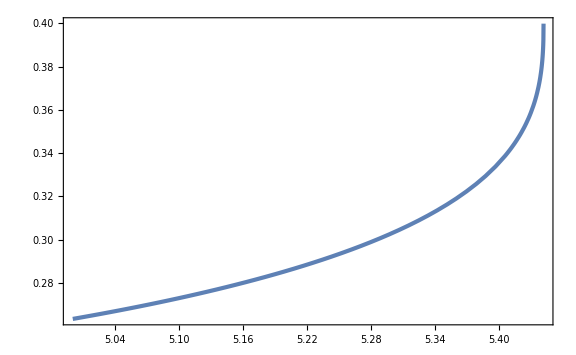

```mathematica
Plot[Cbarmfull[γ],{γ,5,γmax}]
```

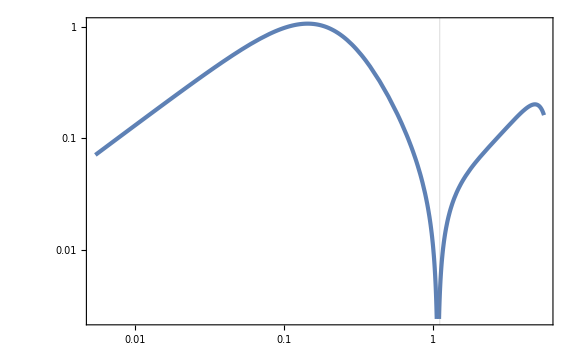

```mathematica
LogLogPlot[Abs[CompactC'[x]/.{μ->(1-dsol[γ])/γ}/.{γ->5.4}],{x,0,5xminγ[5.4]},GridLines->{{xminγ[5.4]},None}]
```

### full num

```mathematica
γ=544/100;
```

```mathematica
zetabar[x_,mu_]=-1/γ Log[1-γ mu Sinc[x]]//Simplify
```

-25/136 Log[1-136/25 mu Sinc[x]]

```mathematica
CompactC[x_,mu_]=2/3(1-(1+x D[zetabar[x,mu], x])^2)//Simplify
```

2/3 (1-(1+(25 mu (-x Cos[x]+Sin[x]))/(x (-25+136 mu Sinc[x])))^2)

```mathematica
rmcond[x_,mu_]=-1/(mu x^2)(D[zetabar[x,mu], x]+x D[D[zetabar[x,mu], x], x])//Simplify
```

-1/(x^5 (25-136 mu Sinc[x])^2)25 (136 mu x^2 Cos[x]^2+Sin[x] (25 x-25 x^3+136 mu Sin[x])-x Cos[x] (25 x+272 mu Sin[x])+136 mu x (x Cos[x]+(-1+x^2) Sin[x]) Sinc[x])

```mathematica
xmList=Table[{10^logmu,x/.FindRoot[rmcond[x,(1-10^logmu)/γ]==0,{x,10^-5},WorkingPrecision->30]},{logmu,-15,-2,10^-2}];
```

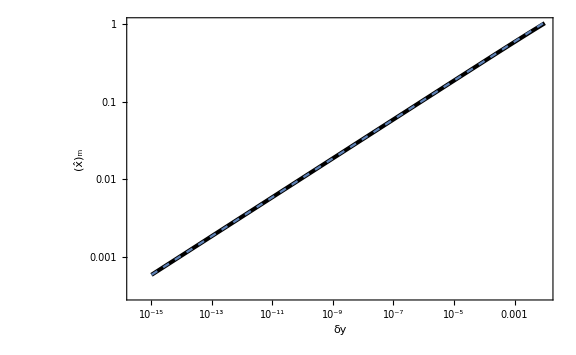

```mathematica
Show[ListLogLogPlot[xmList,FrameLabel->{δy,Subscript[OverHat[x], "m"]},PlotStyle->{AbsoluteThickness[3],Black},PlotRange->Full],LogLogPlot[xm[d],{d,10^-15,10^-2},PlotStyle->Dashed]]
```

```mathematica
xmint[dy_]=Interpolation[xmList][dy];
```

```mathematica
Rarea[x_,mu_]=E^zetabar[x,mu] x;
```

```mathematica
VMS[mu_]=(4π)/3 Rarea[xmint[1-γ mu],mu]^3;
```

```mathematica
Cbarmn[mu_]:=1/VMS[mu] 4π NIntegrate[CompactC[x,mu] Rarea[x,mu]^2 D[Rarea[x,mu], x],{x,0,xmint[1-γ mu]},WorkingPrecision->30]
```

```mathematica
Cbarmn[(1-10^-10)/γ]
```

0.4000585917980111540907408

```mathematica
CbarmList=Table[{10^logmu,Cbarmn[(1-10^logmu)/γ]-2/5},{logmu,-15,-2,10^-2}];//AbsoluteTiming
```

{46.1966,Null}

```mathematica
Cbarint[dy_]=Interpolation[CbarmList][dy];
```

```mathematica
dysol=dy/.FindRoot[Cbarint[dy]==0,{dy,10^-9},WorkingPrecision->30]
```

1.27668645801791002419272458779×10^-9

```mathematica
Cbarint[dysol]
```

1.2×10^-23

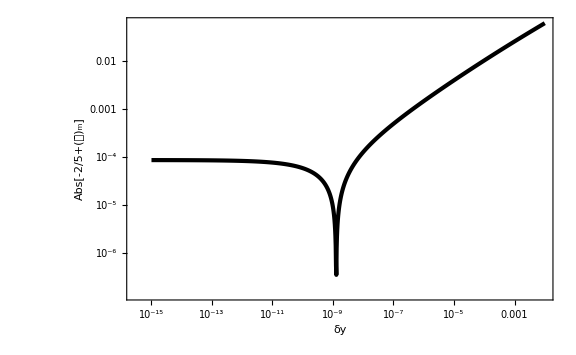

```mathematica
(*Show[*)ListLogLogPlot[Abs[CbarmList],PlotRange->Full,FrameLabel->{δy,Abs[Subscript[OverBar[𝒞], "m"]-2/5]},PlotStyle->{Black,AbsoluteThickness[3]},GridLines->{{dysol},{Cm[γ]-2/5}}](*,LogLogPlot[Abs[Cbarm[d]-2/5],{d,10^-10,10^-2},PlotRange->Full,PlotStyle->Dashed]]*)
```

## Gumbel different limit

```mathematica
zeta[x_]=-1/γ Log[1-γ μ Sinc[x]];
```

```mathematica
CompactC[x_]=2/3(1-(1+x zeta'[x])^2)//Simplify
```

2/3 (1-(1+(μ (x Cos[x]-Sin[x]))/(x-x γ μ Sinc[x]))^2)

```mathematica
Normal[Series[CompactC[x],{x,0,2}]]
```

-(4 x^2 μ)/(9 (-1+γ μ))

```mathematica
rmcond[x_]=zeta'[x]+x zeta''[x]//Simplify
```

1/(x^3 (-1+γ μ Sinc[x])^2)μ (x^2 γ μ Cos[x]^2+Sin[x] (x-x^3+γ μ Sin[x])-x Cos[x] (x+2 γ μ Sin[x])+x γ μ (x Cos[x]+(-1+x^2) Sin[x]) Sinc[x])

```mathematica
xm[d_]=Normal[Series[x/.Solve[Normal[Series[rmcond[x]==0/.{μ->(1-d)/γ},{d,0,1},{x,0,1}]]//Simplify,x][[4]],{d,0,1}]]
```

2^(3/4) 15^(1/4) d^(1/4)

```mathematica
Cm[γ_]=Normal[Series[CompactC[xm[d]]/.{μ->(1-d)/γ},{d,0,0}]]//Simplify
```

(8 (-1+γ))/(3 γ^2)

```mathematica
Plot[Cm[γ],{γ,1,10}]
```

-Graphics-

```mathematica
arealR[x_]=x E^zeta[x]
```

x (1-γ μ Sinc[x])^(-1/γ)

```mathematica
Cintegrand[x_]=Normal[Series[CompactC[x] arealR[x]^2 arealR'[x]/.{μ->(1-d)/γ},{x,xm[d],2},{d,0,1}]]
```

(2^(19/4-3/(2 γ)) 3^(-3/4+3/(2 γ)) 5^(1/4-3/(2 γ)) d^(1/4-3/(2 γ)) (-2^(3/4) 15^(1/4) d^(1/4)+x) (-3+γ) (-2+γ) (-1+γ))/γ^4+(2^(3-3/(2 γ)) 3^(-1+3/(2 γ)) 5^(-3/2/γ) d^(-3/2/γ) (-2^(3/4) 15^(1/4) d^(1/4)+x)^2 (-2+γ) (-1+γ) (18-9 γ+γ^2))/γ^5+d^(-3/2/γ) ((2^(9/2-3/(2 γ)) 3^(-1/2+3/(2 γ)) 5^(1/2-3/(2 γ)) √d (-2+γ) (-1+γ))/γ^3-(2^(5-3/(2 γ)) 3^(1/γ) 5^(-3/2/γ) d (2 3^(1+1/(2 γ))-2 3^(1+1/(2 γ)) γ+3^(1/2/γ) γ^2))/γ^3)

```mathematica
Cbarm[γ_]=Normal[Series[3/arealR[xm[d]]^3 Integrate[Cintegrand[x],{x,0,xm[d]}]/.{μ->(1-d)/γ},{d,0,1}]]
```

-(8 √(6/5) √d (6-6 γ+γ^2))/γ^3-(48 d (36-54 γ+20 γ^2-3 γ^3+γ^4))/(7 γ^6)+(8 (36-54 γ+20 γ^2-3 γ^3+γ^4))/(3 γ^5)

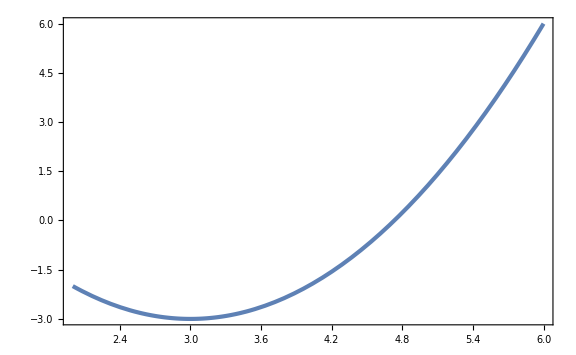

```mathematica
Plot[6-6γ+γ^2,{γ,2,6}]
```

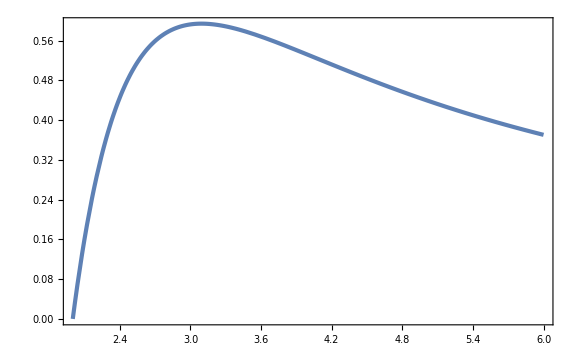

```mathematica
Plot[Cbarm[γ],{γ,2,6},GridLines->{None,{2/5}}]
```

```mathematica
γmax=γ/.Solve[Cbarm[γ]==2/5,γ][[3]]
```

Root5.54Root[-720+1080 #1-400 #1^2+60 #1^3-20 #1^4+3 #1^5&,3]5.538303269510713

```mathematica
γmax//N
```

5.5383

```mathematica
dsol[γ_]=d/.Solve[Cbarm[d]==2/5,d][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

((5/3)^(-1/2-3/(2 γ)) 2^(-5/2-3/(2 γ)) γ)^(-(2 γ)/(3+γ))

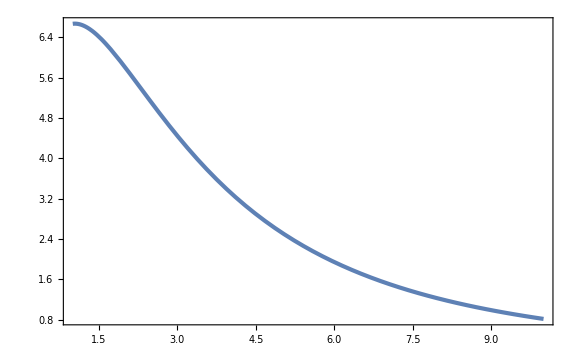

```mathematica
Plot[dsol[γ],{γ,1,10}]
```

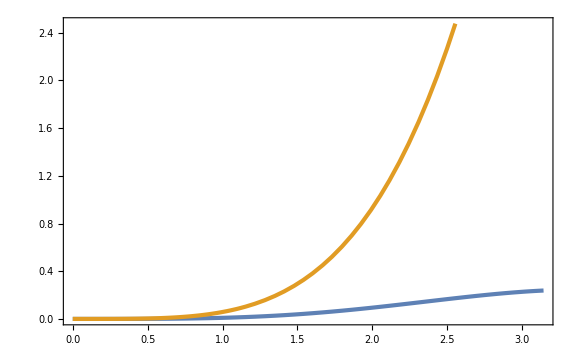

```mathematica
Plot[{CompactC[x] arealR[x]^2 arealR'[x]/.{μ->(1-dsol[γ])/γ}/.{γ->10},Cintegrand[x]/.{d->dsol[γ]}/.{γ->10}},{x,0,xm[dsol[10]]}]
```

```mathematica
Cint[x_,γ_]=CompactC[x] arealR[x]^2 arealR'[x]/.{μ->(1-dsol[γ])/γ}//Simplify
```

2/3 x^2 (1+(-1+((3/5)^((3+γ)/(2 γ)) 2^(-(3+5 γ)/(2 γ)) γ)^(-(2 γ)/(3+γ))) Sinc[x])^(-3/γ) (1+((1-((3/5)^((3+γ)/(2 γ)) 2^(-(3+5 γ)/(2 γ)) γ)^(-(2 γ)/(3+γ))) (x Cos[x]-Sin[x]))/(x (γ+γ (-1+((3/5)^((3+γ)/(2 γ)) 2^(-(3+5 γ)/(2 γ)) γ)^(-(2 γ)/(3+γ))) Sinc[x]))) (1-(1+((1-((3/5)^((3+γ)/(2 γ)) 2^(-(3+5 γ)/(2 γ)) γ)^(-(2 γ)/(3+γ))) (x Cos[x]-Sin[x]))/(γ (x+x (-1+((3/5)^((3+γ)/(2 γ)) 2^(-(3+5 γ)/(2 γ)) γ)^(-(2 γ)/(3+γ))) Sinc[x])))^2)

```mathematica
xminγ[γ_]=xm[dsol[γ]]
```

2^(3/4) 15^(1/4) (((5/3)^(-1/2-3/(2 γ)) 2^(-5/2-3/(2 γ)) γ)^(-(2 γ)/(3+γ)))^(1/4)

```mathematica
Rm[γ_]=arealR[xminγ[γ]]/.{μ->(1-dsol[γ])/γ}
```

2^(3/4) 15^(1/4) (((5/3)^(-1/2-3/(2 γ)) 2^(-5/2-3/(2 γ)) γ)^(-(2 γ)/(3+γ)))^(1/4) (1-(1-((5/3)^(-1/2-3/(2 γ)) 2^(-5/2-3/(2 γ)) γ)^(-(2 γ)/(3+γ))) Sinc[2^(3/4) 15^(1/4) (((5/3)^(-1/2-3/(2 γ)) 2^(-5/2-3/(2 γ)) γ)^(-(2 γ)/(3+γ)))^(1/4)])^(-1/γ)

```mathematica
Cbarmfull[γ_]:=NIntegrate[Cint[x,γ],{x,0,xminγ[γ]}] 3/Rm[γ]^3
```

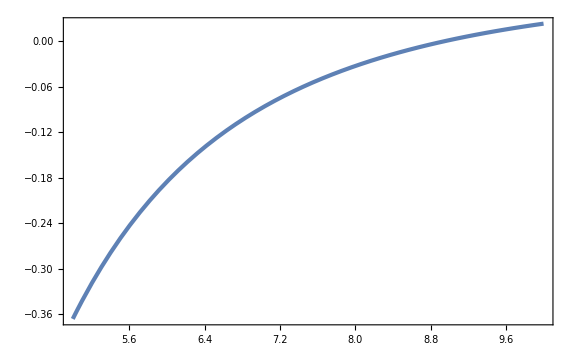

```mathematica
Plot[Cbarmfull[γ],{γ,5,10}]
```

```mathematica
LogLogPlot[Abs[CompactC'[x]/.{μ->(1-dsol[γ])/γ}/.{γ->5.4}],{x,0,5xminγ[5.4]},GridLines->{{xminγ[5.4]},None}]
```

-Graphics-

## quadratic

```mathematica
DSolve[x''[NN]-3x'[NN]+3η x[NN]==0,x[NN],NN]
```

{{x[NN]→ⅇ^(1/2 NN (3-√3 √(3-4 η))) C[1]+ⅇ^(1/2 NN (3+√3 √(3-4 η))) C[2]}}

```mathematica
$Assumptions={λp∈Reals,λm∈Reals,NN-Ns>0};
```

```mathematica
xsol[NN_]=Cp E^(λp(NN-Ns))+Cm E^(λm(NN-Ns));
```

```mathematica
(-xsol'[Ns]+λm xsol[Ns])/(λp-λm)//Simplify
```

-Cp

```mathematica
(-xsol'[NN]+λm xsol[NN])/(-xsol'[Ns]+λm xsol[Ns])//Simplify
```

ⅇ^((NN-Ns) λp)

```mathematica
1/λp Log[(-xsol'[NN]+λm xsol[NN])/(-xsol'[Ns]+λm xsol[Ns])]//FullSimplify
```

NN-Ns

```mathematica
((-xsol'[NN]+λp xsol[NN])/(-xsol'[Ns]+λp xsol[Ns]))^λp//Simplify
((-xsol'[NN]+λm xsol[NN])/(-xsol'[Ns]+λm xsol[Ns]))^λm//Simplify
```

ⅇ^((NN-Ns) λm λp)

ⅇ^((NN-Ns) λm λp)